# Coding Challenge Effect of shifting reduced rank matrix on value of determinant

### Implementation of Udemy coding challenge originally done in Matlab

#### 1 Generate a square random matrix (say 20x20) 2 Impose a linear dependence (reduce rank matrix) 3 “shift” the matrix (0 -> 0.1 * identity matrix). 4 Compute the abs(determinant) of the shifted matrix 5 Repeat the above 1000 times for each shift value, take an average of the abs(determinant) 6 Plot the avg abs determinant vs shift amount

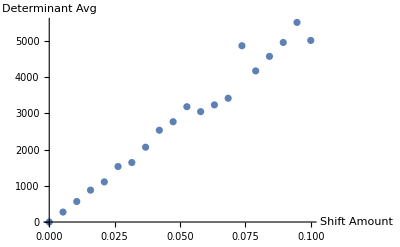

```mathematica
ShiftList = Array[#&,20,{0,0.1}];
ShiftListLen = Length[ShiftList];
(* Create the array that will hold the determinant results *)
DetRes = RandomInteger[0, {ShiftListLen,2}];

For [shiftIdx = 1, shiftIdx ≤ ShiftListLen, shiftIdx ++,
ShiftMatrix = IdentityMatrix[20]*ShiftList[[shiftIdx]];
DeterminantAvg = 0;
For [runIdx = 1, runIdx ≤ 1000, runIdx++,
(* Generate a square random matrix 20x20 *)
M1  = RandomReal[2.0,{20,20}];

(* Impose a linear dependence (reduce the rank) 
  Copy row 2 to row 1 *)
M1[[1]] = M1[[2,All]];
(* ReducedRankDet = Det[M1];*)
M1 = M1 + ShiftMatrix;
DeterminantAvg += Abs[Det[M1]];
];

DeterminantAvg = DeterminantAvg / runIdx;
DetRes[[shiftIdx,1]] = ShiftList[[shiftIdx]];
DetRes[[shiftIdx,2]] = DeterminantAvg;
];
ListPlot[DetRes,AxesLabel->{"Shift Amount", "Determinant Avg"}]
```